```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
ρ1[x_,rx_,ry_,n_]:=ry (1-Abs[x/rx]^n)^(1/n)
ρ2[x_,rx_,ry_,n_]:=-ry (1-Abs[x/rx]^n)^(1/n)
```

```mathematica
Export["LameEllipse.eps",
Plot[{ρ1[x,3,1,0.5],ρ1[x,3,1,1],ρ1[x,3,1,2],ρ1[x,3,1,5],ρ2[x,3,1,0.5],ρ2[x,3,1,1],ρ2[x,3,1,2],ρ2[x,3,1,5]},{x,-3,3},PlotRange->All,ImageSize->Large,LabelStyle->Directive[{Black,FontSize->22}],AxesLabel->{"x_1","x_2"},PlotStyle->{Black,{Black,Dashing[0.025]},{Black,DotDashed},{Black,Dashing[0.05]}},PlotLegends->{"n = 0.5", "n = 1", "n = 2", "n = 5"}]
]
```

LameEllipse.eps

```mathematica
ρ[x_,y_,rx_,ry_,n_]:=(Abs[x/rx]^n+Abs[y/ry]^n)^(1/n)
ϕ[x_,y_,p_,q_,rx_,ry_,n_]:=Piecewise[{{(p n)/(4rx ry Beta[1/n,1/n] Beta[2/p,q+1])(1-(Abs[x/rx]^n+Abs[y/ry]^n)^(p/n))^q, Abs[x/rx]^n+Abs[y/ry]^n≤1}, {0, Abs[x/rx]^n+Abs[y/ry]^n>1}}]
```

```mathematica
N0=10;
Msh={Table[Line[{{0,n/N0},{1,n/N0}}],{n,0,N0}],Table[Line[{{n/N0,0},{n/N0,1}}],{n,0,N0}]};
points=Table[{Point[{{0.025+n/N0,0.025+m/N0},{0.025+n/N0,0.075+m/N0},{0.075+n/N0,0.025+m/N0},{0.075+n/N0,0.075+m/N0}}]},{n,0,N0-1},{m,0,N0-1}];
circ=Circle[{0.075+4/N0,0.075+7/N0},0.21];
cros={Line[{{0.075+4/N0-0.01,0.075+7/N0-0.01},{0.075+4/N0+0.01,0.075+7/N0+0.01}}],Line[{{0.075+4/N0-0.01,0.075+7/N0+0.01},{0.075+4/N0+0.01,0.075+7/N0-0.01}}]};
approx={Rectangle[{0.3,0.6},{0.7,0.9}],Rectangle[{0.3,0.9},{0.6,1}],Rectangle[{0.2,0.7},{0.3,0.9}],Rectangle[{0.4,0.5},{0.6,0.6}]};
(*Export["ApproxSQ.eps",*)
Graphics[{Thick,Msh,points,cros,Opacity[0.2],approx,Opacity[1],Thickness[0.006], circ},ImageSize->Large]
```

ApproxSQ.eps

```mathematica
N0=10;
Msh={Table[Line[{{0,n/N0},{1,n/N0}}],{n,0,N0}],Table[Line[{{n/N0,0},{n/N0,1}}],{n,0,N0}]};
points=Table[Point[{0.05+n/N0,0.05+m/N0}],{n,0,N0-1},{m,0,N0-1}];
circ=Circle[{0.05+4/N0,0.05+7/N0},0.21];
cros={Line[{{0.05+4/N0-0.01,0.05+7/N0-0.01},{0.05+4/N0+0.01,0.05+7/N0+0.01}}],Line[{{0.05+4/N0-0.01,0.05+7/N0+0.01},{0.05+4/N0+0.01,0.05+7/N0-0.01}}]};
approx={Rectangle[{0.3,0.6},{0.6,0.9}],Rectangle[{0.2,0.7},{0.3,0.8}],Rectangle[{0.6,0.7},{0.7,0.8}],Rectangle[{0.4,0.5},{0.5,0.6}],Rectangle[{0.4,0.9},{0.5,1.0}]};
Export["ApproxS.eps",
Graphics[{Thick,Msh,points,cros,Opacity[0.2],approx,Opacity[1],Thickness[0.006], circ},ImageSize->Large]
]
```

ApproxS.eps

```mathematica
Export["OpenMPAcceleration.eps",
BarChart[{{
Labeled[1.8,Rotate["2500",0],Top],
Labeled[3.3,Rotate["10000",90 Degree],Center],
Labeled[6.2,Rotate["40000",π/2],Bottom],
Labeled[14.3,Rotate["2500, r = 0.1",π/2],Bottom],
Labeled[15,Rotate["10000, r = 0.1",π/2],Bottom],
Labeled[15.3,Rotate["40000, r = 0.1",π/2],Bottom],
Labeled[14.9,Rotate["2500, r = 0.2",π/2],Bottom],
Labeled[15.4,Rotate["10000, r = 0.2",π/2],Bottom],
Labeled[15.5,Rotate["40000, r = 0.2",π/2],Bottom]
}},ImageSize->Large,LabelStyle->Directive[{Black,FontSize->22}],AxesLabel->{"","t_1/t_16"},LabelingFunction->Above,ChartStyle->Directive[EdgeForm[{Thick,Black}], White]]
]
```

OpenMPAcceleration.eps

```mathematica
Export["MPIAcceleration.eps",
BarChart[{{
Labeled[2.9,Rotate["10000, r = 0.1, mem",π/2],Bottom],
Labeled[3.1,Rotate["10000, r = 0.2, mem",π/2],Bottom],
Labeled[2.9,Rotate["40000, r = 0.1, mem",π/2],Bottom],
Labeled[3,Rotate["40000, r = 0.2, mem",π/2],Bottom],
Labeled[3.4,Rotate["10000, r = 0.1, speed",π/2],Bottom],
Labeled[3.5,Rotate["40000, r = 0.1, speed",π/2],Bottom],
Labeled[3.5,Rotate["10000, r = 0.2, speed",π/2],Bottom],
Labeled[3.5,Rotate["40000, r = 0.2, speed",π/2],Bottom]
}},ImageSize->Large,LabelStyle->Directive[{Black,FontSize->22}],AxesLabel->{"","t_16/max_p t_16^p"},LabelingFunction->Above,ChartStyle->Directive[EdgeForm[{Thick,Black}], White]]
]
```

MPIAcceleration.eps

```mathematica
(*Time speed balancing*)
Export["TimeSpeedBalancing.eps",
PieChart[{71.63,75.31,77.42,86.76},ImageSize->Large,LabelStyle->Directive[{Black,FontSize->22}],ChartStyle->Directive[EdgeForm[{Thick,Black}], White],ChartLabels->{"t_16^1 = 72 s","t_16^2 = 75 s","t_16^3 = 77 s","t_16^4 = 87 s"}]
]
```

TimeSpeedBalancing.eps

```mathematica
(*Memory speed balancing*)
Export["MemorySpeedBalancing.eps",
PieChart[{8.8,8.7,8.9,20.6},ImageSize->Large,LabelStyle->Directive[{Black,FontSize->22}],ChartStyle->Directive[EdgeForm[{Thick,Black}], White],ChartLabels->{"V_1 = 8.8 Gb","V_2 = 8.7 Gb","V_3 = 8.9 Gb","V_4 = 20.6 Gb"}]
]
```

MemorySpeedBalancing.eps

```mathematica
(*Time memory balancing*)
Export["TimeMemoryBalancing.eps",
PieChart[{95.76,99.08,60.50,50.03},ImageSize->Large,LabelStyle->Directive[{Black,FontSize->22}],ChartStyle->Directive[EdgeForm[{Thick,Black}], White],ChartLabels->{"t_16^1 = 96 s","t_16^2 = 99 s","t_16^3 = 61 s","t_16^4 = 50 s"}]]
```

TimeMemoryBalancing.eps

```mathematica
(*Memory memory balancing*)
Export["MemoryMemoryBalancing.eps",
PieChart[{11.6,11.7,11.9,11.8},ImageSize->Large,LabelStyle->Directive[{Black,FontSize->22}],ChartStyle->Directive[EdgeForm[{Thick,Black}], White],ChartLabels->{"V_1 = 11.6 Gb","V_2 = 11.7 Gb","V_3 = 11.9 Gb","V_4 = 11.9 Gb"}]]
```

MemoryMemoryBalancing.eps

```mathematica
f1[x_]:=1;
f2[x_]:=Piecewise[{{4x, x≤0.5}, {4-4x, x>0.5}}];
f3[x_]:=Piecewise[{{2-4x, x≤0.5}, {4x-2, x>0}}];
```

```mathematica
rect=Line[{{0,0},{10,0},{10,1},{0,1},{0,0}}];
M0=10;
FZ=22;
LeftP=Table[Arrow[{{0,n/M0},{-0.5*f1[n/M0],n/M0}}],{n,0,M0}];
RightP=Table[Arrow[{{10,n/M0},{10+0.5*f1[n/M0],n/M0}}],{n,0,M0}];
Lline=Line[{{-0.5,0},{-0.5,1}}];
Rline=Line[{{10.5,0},{10.5,1}}];
σnL=Text[Style["σ̂·n = -f_1((x̄)_2)",FZ],{-0.1,1.35}];
σnR=Text[Style["σ̂·n = f_1((x̄)_2)",FZ],{10.1,1.35}];
AB={Line[{{0,0.5},{10,0.5}}],Text[Style["A",FZ],{0.3,0.7}],Text[Style["B",FZ],{9.7,0.7}],PointSize[0.015],Point[{0,0.5}],Point[{10,0.5}]};
CD={Line[{{5,0},{5,1}}],Text[Style["C",FZ],{5.3,0.2}],Text[Style["D",FZ],{5.3,0.73}],PointSize[0.015],Point[{5,0}],Point[{5,1}]};
Export["LongRectF1.eps",
Graphics[{Thick,Arrowheads[0.01],rect,LeftP,RightP,σnL,σnR(*,AB,CD*)},ImageSize->Large]]
```

LongRectF1.eps

```mathematica
rect=Line[{{0,0},{10,0},{10,1},{0,1},{0,0}}];
M0=10;
FZ=22;
LeftP=Table[Arrow[{{0,n/M0},{-0.5*f2[n/M0],n/M0}}],{n,0,M0}];
RightP=Table[Arrow[{{10,n/M0},{10+0.5*f2[n/M0],n/M0}}],{n,0,M0}];
Lline=Line[{{0,0},{-1,0.5},{0,1}}];
Rline=Line[{{10,0},{11,0.5},{10,1}}];
σnL=Text[Style["σ̂·n = -f_2((x̄)_2)",FZ],{-0.1,1.35}];
σnR=Text[Style["σ̂·n = f_2((x̄)_2)",FZ],{10.1,1.35}];
AB={Line[{{0,0.5},{10,0.5}}],Text[Style["A",FZ],{0.3,0.7}],Text[Style["B",FZ],{9.7,0.7}],PointSize[0.015],Point[{0,0.5}],Point[{10,0.5}]};
CD={Line[{{5,0},{5,1}}],Text[Style["C",FZ],{5.3,0.2}],Text[Style["D",FZ],{5.3,0.73}],PointSize[0.015],Point[{5,0}],Point[{5,1}]};
Export["LongRectF2.eps",
Graphics[{Thick,Arrowheads[0.01],rect,LeftP,RightP,σnL,σnR(*,AB,CD*)},ImageSize->Large]]
```

LongRectF2.eps

```mathematica
rect=Line[{{0,0},{10,0},{10,1},{0,1},{0,0}}];
M0=10;
FZ=22;
LeftP=Table[Arrow[{{0,n/M0},{-0.5*f3[n/M0],n/M0}}],{n,0,M0}];
RightP=Table[Arrow[{{10,n/M0},{10+0.5*f3[n/M0],n/M0}}],{n,0,M0}];
Lline=Line[{{-1,0},{0,0.5},{-1,1}}];
Rline=Line[{{11,0},{10,0.5},{11,1}}];
σnL=Text[Style["σ̂·n = -f_3((x̄)_2)",FZ],{-0.1,1.35}];
σnR=Text[Style["σ̂·n = f_3((x̄)_2)",FZ],{10.1,1.35}];
AB={Line[{{0,0.5},{10,0.5}}],Text[Style["A",FZ],{0.3,0.7}],Text[Style["B",FZ],{9.7,0.7}],PointSize[0.015],Point[{0,0.5}],Point[{10,0.5}]};
CD={Line[{{5,0},{5,1}}],Text[Style["C",FZ],{5.3,0.2}],Text[Style["D",FZ],{5.3,0.73}],PointSize[0.015],Point[{5,0}],Point[{5,1}]};
Export["LongRectF3.eps",
Graphics[{Thick,Arrowheads[0.01],rect,LeftP,RightP,σnL,σnR(*,AB,CD*)},ImageSize->Large]]
```

LongRectF3.eps

```mathematica
Export["AppLoadF.eps",
Plot[{1,Piecewise[{{4x, x≤0.5}, {4-4x, x>0.5}}],Piecewise[{{2-4x, x≤0.5}, {4x-2, x>0}}]},{x,0,1},ImageSize->Large,LabelStyle->Directive[{Black,FontSize->22}],AxesLabel->{"x","f"},PlotStyle->{Black,{Black,Dashing[0.025]},{Black,DotDashed},{Black,Dashing[0.05]}},PlotLegends->{"f = f_1", "f = f_2", "f = f_3"}]
]
```

AppLoadF.eps

```mathematica
σ11Uniform=Interpolation[Import["data/LongRect/LongRect_nonloc_p12_r02/sigma11.csv"]];
σ11Triangle=Interpolation[Import["data/LongRect/LongRect_nonloc_p12_r02_triangle/sigma11.csv"]];
σ11InvTriangle=Interpolation[Import["data/LongRect/LongRect_nonloc_p12_r02_inv_triangle/sigma11.csv"]];
σ11ShortUniform=Interpolation[Import["data/LongRect/LongRect_nonloc_p12_r02_short_uniform/sigma11.csv"]];
```

Interpolation::udeg: Interpolation on unstructured grids is currently only supported for InterpolationOrder->1 or InterpolationOrder->All. Order will be reduced to 1.

```mathematica
y0=0.;
Export["LongRectStress11VarFx200.eps",
Show[
Plot[{σ11Uniform[x,y0],σ11Triangle[x,y0],σ11InvTriangle[x,y0]},{x,0,10},PlotRange->Full,ImageSize->Large,LabelStyle->Directive[{Black,FontSize->22}],AxesLabel->{"x_1","(σ̄)_11"},PlotStyle->{Black,{Black,Dashing[0.05]},{Black,DotDashed},{Black,Dashing[0.05]}},PlotLegends->Placed[{"f_1","f_2","f_3","f_4"},Scaled[{0.7,0.8}]]],
Graphics[{Text[Style["r = 0.2",22],Scaled[{0.35,0.95}]],Text[Style["x_2 = 0",22],Scaled[{0.35,0.85}]],Text[Style["φ = φ_(2, 1)",22],Scaled[{0.35,0.75}]],Text[Style["p_1 = 1/2",22],Scaled[{0.35,0.65}]]}]
]
]
```

LongRectStress11VarFx200.eps

```mathematica
σ11Loc=Interpolation[Import["data/LongRect/LongRect_loc/sigma11.csv"]];
σ11p12r005=Interpolation[Import["data/LongRect/LongRect_nonloc_p12_r005/sigma11.csv"]];
σ11p12r01=Interpolation[Import["data/LongRect/LongRect_nonloc_p12_r01/sigma11.csv"]];
σ11p12r02=Interpolation[Import["data/LongRect/LongRect_nonloc_p12_r02/sigma11.csv"]];
```

Interpolation::udeg: Interpolation on unstructured grids is currently only supported for InterpolationOrder->1 or InterpolationOrder->All. Order will be reduced to 1.

```mathematica
Export["LongRectStress11VarR.eps",
Show[
Plot[{σ11Loc[5,y],σ11p12r005[5,y],σ11p12r01[5,y],σ11p12r02[5,y]},{y,0,1},PlotRange->Full,ImageSize->Large,LabelStyle->Directive[{Black,FontSize->22}],AxesLabel->{"x_2","(σ̄)_11"},PlotStyle->{{Black,Dashing[0.05]},Black,{Black,DotDashed},{Black,Dashing[0.025]}},PlotLegends->Placed[{"r = 0","r = 0.05","r = 0.1","r = 0.2"},Scaled[{0.7,0.5}]]],
Graphics[{Text[Style["x_1 = 5",22],Scaled[{0.35,0.69}]],Text[Style["φ = φ_(2, 1)",22],Scaled[{0.35,0.52}]],Text[Style["p_1 = 1/2",22],Scaled[{0.35,0.35}]]}]
]
]
```

LongRectStress11VarR.eps

```mathematica
σ11Loc=Interpolation[Import["data/LongRect/LongRect_loc/sigma11.csv"]];
σ11p23r01=Interpolation[Import["data/LongRect/LongRect_nonloc_p23_r01/sigma11.csv"]];
σ11p12r01=Interpolation[Import["data/LongRect/LongRect_nonloc_p12_r01/sigma11.csv"]];
σ11p13r01=Interpolation[Import["data/LongRect/LongRect_nonloc_p13_r01/sigma11.csv"]];
```

Interpolation::udeg: Interpolation on unstructured grids is currently only supported for InterpolationOrder->1 or InterpolationOrder->All. Order will be reduced to 1.

```mathematica
Export["LongRectStress11VarP.eps",
Show[
Plot[{σ11Loc[5,y],σ11p23r01[5,y],σ11p12r01[5,y],σ11p13r01[5,y]},{y,0,1},PlotRange->Full,ImageSize->Large,LabelStyle->Directive[{Black,FontSize->22}],AxesLabel->{"x_2","(σ̄)_11"},PlotStyle->{{Black,Dashing[0.05]},Black,{Black,DotDashed},{Black,Dashing[0.025]}},PlotLegends->Placed[{"p_1 = 1","p_1 = 2/3","p_1 = 1/2","p_1 = 1/3"},Scaled[{0.7,0.5}]]],
Graphics[{Text[Style["x_1 = 5",22],Scaled[{0.35,0.69}]],Text[Style["φ = φ_(2, 1)",22],Scaled[{0.35,0.52}]],Text[Style["r = 0.1",22],Scaled[{0.35,0.35}]]}]
]
]
```

LongRectStress11VarP.eps

```mathematica
σ12Loc=Interpolation[Import["data/LongRect/LongRect_loc/sigma12.csv"]];
σ12p23r01=Interpolation[Import["data/LongRect/LongRect_nonloc_p23_r01/sigma12.csv"]];
σ12p12r01=Interpolation[Import["data/LongRect/LongRect_nonloc_p12_r01/sigma12.csv"]];
σ12p13r01=Interpolation[Import["data/LongRect/LongRect_nonloc_p13_r01/sigma12.csv"]];
```

Interpolation::udeg: Interpolation on unstructured grids is currently only supported for InterpolationOrder->1 or InterpolationOrder->All. Order will be reduced to 1.

```mathematica
Export["LongRectSigma12X1.eps",
Show[
Plot[{σ12p23r01[x,0.1],σ12p12r01[x,0.1],σ12p13r01[x,0.1]},{x,0,10},PlotRange->Full,ImageSize->Large,LabelStyle->Directive[{Black,FontSize->22}],AxesLabel->{"x_1","(σ̄)_12"},PlotStyle->{{Black,DotDashed},Black,{Black,Dashing[0.025]}},PlotLegends->Placed[{"p_1 = 2/3","p_1 = 1/2","p_1 = 1/3"},Scaled[{0.7,0.78}]]],
Graphics[{Text[Style["x_2 = 0.1",22],Scaled[{0.35,0.96}]],Text[Style["r = 0.1",22],Scaled[{0.35,0.84}]],Text[Style["φ = φ_(2, 1)",22],Scaled[{0.35,0.72}]],Text[Style["f = f_1",22],Scaled[{0.35,0.6}]]}]
]
]
```

LongRectSigma12X1.eps

```mathematica
Export["LongRectSigma12X2.eps",
Show[
Plot[{σ12Loc[0.1,y],σ12p23r01[0.1,y],σ12p12r01[0.1,y],σ12p13r01[0.1,y]},{y,0,1},PlotRange->Full,ImageSize->Large,LabelStyle->Directive[{Black,FontSize->22}],AxesLabel->{"x_2","(σ̄)_11"},PlotStyle->{{Black,Dashing[0.05]},Black,{Black,DotDashed},{Black,Dashing[0.025]}},PlotLegends->Placed[{"p_1 = 2/3","p_1 = 1/2","p_1 = 1/3"},Scaled[{0.7,0.8}]]],
Graphics[{Text[Style["x_2 = 0.1",22],Scaled[{0.35,0.96}]],Text[Style["r = 0.1",22],Scaled[{0.35,0.84}]],Text[Style["φ = φ_(2, 1)",22],Scaled[{0.35,0.72}]],Text[Style["f = f_1",22],Scaled[{0.35,0.6}]]}]
]
]
```

LongRectSigma12X2.eps

```mathematica
ϵ11Loc=Interpolation[Import["data/LongRect/LongRect_loc/eps11.csv"]];
ϵ11p12r005=Interpolation[Import["data/LongRect/LongRect_nonloc_p12_r005/eps11.csv"]];
ϵ11p12r01=Interpolation[Import["data/LongRect/LongRect_nonloc_p12_r01/eps11.csv"]];
ϵ11p12r02=Interpolation[Import["data/LongRect/LongRect_nonloc_p12_r02/eps11.csv"]];
```

Interpolation::udeg: Interpolation on unstructured grids is currently only supported for InterpolationOrder->1 or InterpolationOrder->All. Order will be reduced to 1.

```mathematica
y0=0.5;
Export["LongRectEps11VarR.eps",
Show[
Plot[{ϵ11Loc[x,y0],ϵ11p12r005[x,y0],ϵ11p12r01[x,y0],ϵ11p12r02[x,y0]},{x,0,1.5},PlotRange->Full,ImageSize->Large,LabelStyle->Directive[{Black,FontSize->22}],AxesLabel->{"x_1","(ϵ̄)_11"},PlotStyle->{{Black,Dashing[0.05]},Black,{Black,DotDashed},{Black,Dashing[0.025]}},PlotLegends->Placed[{"r = 0","r = 0.05","r = 0.1","r = 0.2"},Scaled[{0.7,0.57}]]],
Graphics[{Text[Style["x_2 = 0.5",22],Scaled[{0.35,0.80}]],Text[Style["φ = φ_(2, 1)",22],Scaled[{0.35,0.5}]],Text[Style["p_1 = 1/2",22],Scaled[{0.35,0.65}]],Text[Style["f = f_1",22],Scaled[{0.35,0.35}]]}]
]
]
```

LongRectEps11VarR.eps

```mathematica
ϵ11Loc=Interpolation[Import["data/LongRect/LongRect_loc/eps11.csv"]];
ϵ11p23r01=Interpolation[Import["data/LongRect/LongRect_nonloc_p23_r01/eps11.csv"]];
ϵ11p12r01=Interpolation[Import["data/LongRect/LongRect_nonloc_p12_r01/eps11.csv"]];
ϵ11p13r01=Interpolation[Import["data/LongRect/LongRect_nonloc_p13_r01/eps11.csv"]];
```

Interpolation::udeg: Interpolation on unstructured grids is currently only supported for InterpolationOrder->1 or InterpolationOrder->All. Order will be reduced to 1.

```mathematica
y0=0.5;
Export["LongRectEps11VarP.eps",
Show[
Plot[{ϵ11Loc[x,y0],ϵ11p23r01[x,y0],ϵ11p12r01[x,y0],ϵ11p13r01[x,y0]},{x,0,1.5},PlotRange->Full,ImageSize->Large,LabelStyle->Directive[{Black,FontSize->22}],AxesLabel->{"x_1","(ϵ̄)_11"},PlotStyle->{{Black,Dashing[0.05]},Black,{Black,DotDashed},{Black,Dashing[0.025]}},PlotLegends->Placed[{"p_1 = 1","p_1 = 2/3","p_1 = 1/2","p_1 = 1/3"},Scaled[{0.7,0.57}]]],
Graphics[{Text[Style["x_2 = 0.5",22],Scaled[{0.35,0.80}]],Text[Style["φ = φ_(2, 1)",22],Scaled[{0.35,0.5}]],Text[Style["p_1 = 1/2",22],Scaled[{0.35,0.65}]],Text[Style["f = f_1",22],Scaled[{0.35,0.35}]]}]
]
]
```

LongRectEps11VarP.eps

```mathematica
u1Loc=Interpolation[Import["data/LongRect/LongRect_loc/u1.csv"]];
u1NonLocP1Q1=Interpolation[Import["data/LongRect/LongRect_nonloc_p12_r02_p1_q1/u1.csv"]];
u1NonLocP3Q1=Interpolation[Import["data/LongRect/LongRect_nonloc_p12_r02_p3_q1/u1.csv"]];
u1NonLocP5Q1=Interpolation[Import["data/LongRect/LongRect_nonloc_p12_r02_p5_q1/u1.csv"]];
u1NonLocConst=Interpolation[Import["data/LongRect/LongRect_nonloc_p12_r02_const/u1.csv"]];
```

Interpolation::udeg: Interpolation on unstructured grids is currently only supported for InterpolationOrder->1 or InterpolationOrder->All. Order will be reduced to 1.

```mathematica
y0=0.0;
Export["LongRectDispVarP.eps",
Show[
Plot[{(u1NonLocP1Q1[x,y0]-u1Loc[x,y0])/u1Loc[10,0],(u1NonLocP3Q1[x,y0]-u1Loc[x,y0])/u1Loc[10,0],(u1NonLocP5Q1[x,y0]-u1Loc[x,y0])/u1Loc[10,0],(u1NonLocConst[x,y0]-u1Loc[x,y0])/u1Loc[10,0]},{x,0,10},PlotRange->Full,ImageSize->Large,LabelStyle->Directive[{Black,FontSize->22}],AxesLabel->{"x_1","((ū)_1^NonLoc)/(max | SubsuperscriptBox[OverscriptBox[u, _], 1, Loc] |)"},PlotStyle->{{Black,DotDashed},Black,{Black,Dashing[0.025]},{Black,Thickness[0.01]}}],
Plot[{-100,-200},{x,0,10},LabelStyle->Directive[{Black,FontSize->22}],PlotStyle->{{Black,DotDashed},Black},
PlotLegends->Placed[{"φ = φ_(1, 1)","φ = φ_(3, 1)"},Scaled[{0.25,0.8}]]],
Plot[{-100,-200},{x,0,10},LabelStyle->Directive[{Black,FontSize->22}],PlotStyle->{{Black,Dashing[0.025]},{Black,Thickness[0.01]}},
PlotLegends->Placed[{"φ = φ_(5, 1)","φ = (π r^2)^-1"},Scaled[{0.6,0.8}]]],
Graphics[{Text[Style["(x̄)_2 = 0",22],Scaled[{0.25,0.2}]],Text[Style["r = 0.2",22],Scaled[{0.45,0.2}]],Text[Style["p_1 = 1/2",22],Scaled[{0.65,0.2}]],Text[Style["f = f_1",22],Scaled[{0.85,0.2}]]}]
]
]
```

LongRectDispVarP.eps

```mathematica
u1Loc=Interpolation[Import["data/LongRect/LongRect_loc/u1.csv"]];
u1NonLocP1Q1=Interpolation[Import["data/LongRect/LongRect_nonloc_p12_r02_p1_q1/u1.csv"]];
u1NonLocP1Q2=Interpolation[Import["data/LongRect/LongRect_nonloc_p12_r02_p1_q2/u1.csv"]];
u1NonLocP1Q3=Interpolation[Import["data/LongRect/LongRect_nonloc_p12_r02_p1_q3/u1.csv"]];
```

Interpolation::udeg: Interpolation on unstructured grids is currently only supported for InterpolationOrder->1 or InterpolationOrder->All. Order will be reduced to 1.

```mathematica
Export["LongRectDispVarQ.eps",
Show[
Plot[{(u1NonLocP1Q1[x,y0]-u1Loc[x,y0])/u1Loc[10,0],(u1NonLocP1Q2[x,y0]-u1Loc[x,y0])/u1Loc[10,0],(u1NonLocP1Q3[x,y0]-u1Loc[x,y0])/u1Loc[10,0]},{x,0,10},PlotRange->Full,ImageSize->Large,LabelStyle->Directive[{Black,FontSize->22}],AxesLabel->{"x_1","((ū)_1^NonLoc)/(max | SubsuperscriptBox[OverscriptBox[u, _], 1, Loc] |)"},PlotStyle->{{Black,DotDashed},Black,{Black,Dashing[0.025]},{Black,Thickness[0.01]}},PlotLegends->Placed[{"φ = φ_(1, 1)","φ = φ_(1, 2)","φ = φ_(1, 3)"},Scaled[{0.4,0.8}]]],
Graphics[{Text[Style["(x̄)_2 = 0",22],Scaled[{0.25,0.2}]],Text[Style["r = 0.2",22],Scaled[{0.45,0.2}]],Text[Style["p_1 = 1/2",22],Scaled[{0.65,0.2}]],Text[Style["f = f_1",22],Scaled[{0.85,0.2}]]}]
]
]
```

LongRectDispVarQ.eps

```mathematica
points={{0,1},{1,1},{1,0.5},{0.75,0.5},{0.75,0},{0.25,0},{0.25,0.5},{0,0.5},{0,1}};
N0=20;
u0=Table[Line[{{n/N0,1},{n/N0+1/N0,1+1/N0}}],{n,0,N0-1}];
M0=5;
P=Table[Arrow[{{0.25+(0.5n)/M0,0},{0.25+(0.5n)/M0,-0.1}}],{n,0,M0}];
AB={Line[{{0.25,0.1},{0.75,0.1}}],Text[Style["A",22],{0.2,0.1}],Text[Style["B",22],{0.8,0.1}]};
CD={Line[{{0.25,0.4},{0.75,0.4}}],Text[Style["C",22],{0.2,0.4}],Text[Style["D",22],{0.8,0.4}]};
EF={Line[{{0,0.52},{1,0.52}}],Text[Style["E",22],{-0.05,0.52}],Text[Style["F",22],{1.05,0.52}]};
GH={Line[{{0,0.98},{1,0.98}}],Text[Style["G",22],{-0.05,0.98}],Text[Style["H",22],{1.05,0.98}]};
σn=Text[Style["σ̂·n = -1",22],{0.5,-0.15}];
u0Text=Text[Style["u = 0",22],{0.5,1.1}];
Export["T/Tarea.eps",
Graphics[{Thick,Line[points],u0,P,AB,CD,EF,σn,u0Text},ImageSize->Large]
]
```

Tarea.eps

```mathematica
σ22Local=Interpolation[Import["data/T/T_loc/sigma22.csv"]];
σ22Nonlocalr005p12=Interpolation[Import["data/T/T_nonloc_p12_r005/sigma22.csv"]];
σ22Nonlocalr015p12=Interpolation[Import["data/T/T_nonloc_p12_r015/sigma22.csv"]];
σ22Nonlocalr01p23=Interpolation[Import["data/T/T_nonloc_p23_r01/sigma22.csv"]];
σ22Nonlocalr01p12=Interpolation[Import["data/T/T_nonloc_p12_r01/sigma22.csv"]];
σ22Nonlocalr01p13=Interpolation[Import["data/T/T_nonloc_p13_r01/sigma22.csv"]];
ϵ22Local=Interpolation[Import["data/T/T_loc/eps22.csv"]];
ϵ22Nonlocalr005p12=Interpolation[Import["data/T/T_nonloc_p12_r005/eps22.csv"]];
ϵ22Nonlocalr015p12=Interpolation[Import["data/T/T_nonloc_p12_r015/eps22.csv"]];
ϵ22Nonlocalr01p23=Interpolation[Import["data/T/T_nonloc_p23_r01/eps22.csv"]];
ϵ22Nonlocalr01p12=Interpolation[Import["data/T/T_nonloc_p12_r01/eps22.csv"]];
ϵ22Nonlocalr01p13=Interpolation[Import["data/T/T_nonloc_p13_r01/eps22.csv"]];
```

Interpolation::udeg: Interpolation on unstructured grids is currently only supported for InterpolationOrder->1 or InterpolationOrder->All. Order will be reduced to 1.

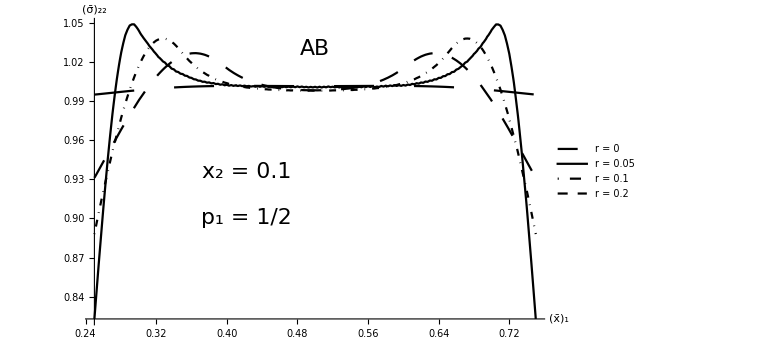

```mathematica
(*AB Var R sigma*)
(*Export["AB_sigma_p12.eps",*)
Show[
Plot[{σ22Local[x,0.1],σ22Nonlocalr005p12[x,0.1],σ22Nonlocalr01p12[x,0.1],σ22Nonlocalr015p12[x,0.1]},{x,0.25,0.75},ImageSize->Large,PlotRange->Full,LabelStyle->Directive[{Black,FontSize->22}],AxesLabel->{"(x̄)_1","(σ̄)_22"},PlotStyle->{{Black,Dashing[0.05]},Black,{Black,DotDashed},{Black,Dashing[0.025]}},PlotLegends->Placed[{"r = 0","r = 0.05","r = 0.1","r = 0.2"},{Scaled[{0.55,0.15}], {0, 0}}]],
Graphics[{Text[Style["p_1 = 1/2",22],Scaled[{0.35,0.35}]],Text[Style["x_2 = 0.1",22],Scaled[{0.35,0.5}]],Text[Style["AB",22],Scaled[{0.5,0.9}]]}]
]
```

```mathematica
(*AB Var P sigma*)
Export["T/AB_sigma_r01.eps",
Show[
Plot[{σ22Local[x,0.1],σ22Nonlocalr01p23[x,0.1],σ22Nonlocalr01p12[x,0.1],σ22Nonlocalr01p13[x,0.1]},{x,0.25,0.75},ImageSize->Large,PlotRange->Full,LabelStyle->Directive[{Black,FontSize->22}],AxesLabel->{"(x̄)_1","(σ̄)_22"},PlotStyle->{{Black,Dashing[0.05]},Black,{Black,DotDashed},{Black,Dashing[0.025]}},PlotLegends->Placed[{"p_1 = 1","p_1 = 2/3","p_1 = 1/2","p_1 = 1/3"},{Scaled[{0.55,0.15}], {0, 0}}]],
Graphics[{Text[Style["r = 0.1",22],Scaled[{0.35,0.4}]],Text[Style["x_2 = 0.1",22],Scaled[{0.35,0.55}]],Text[Style["φ = φ_(2, 1)",22],Scaled[{0.35,0.25}]],Text[Style["AB",22],Scaled[{0.5,0.9}]]}]
]]
```

T/AB_sigma_r01.eps

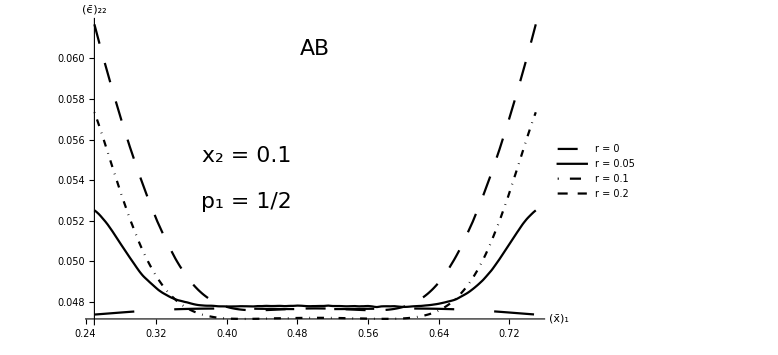

```mathematica
(*Export["AB_eps_p12.eps",*)
Show[
Plot[{ϵ22Local[x,0.1],ϵ22Nonlocalr005p12[x,0.1],ϵ22Nonlocalr01p12[x,0.1],ϵ22Nonlocalr015p12[x,0.1]},{x,0.25,0.75},ImageSize->Large,PlotRange->Full,LabelStyle->Directive[{Black,FontSize->22}],AxesLabel->{"(x̄)_1","(ϵ̄)_22"},PlotStyle->{{Black,Dashing[0.05]},Black,{Black,DotDashed},{Black,Dashing[0.025]}},PlotLegends->Placed[{"r = 0","r = 0.05","r = 0.1","r = 0.2"},{Scaled[{0.55,0.2}], {0, 0}}]],
Graphics[{Text[Style["p_1 = 1/2",22],Scaled[{0.35,0.4}]],Text[Style["x_2 = 0.1",22],Scaled[{0.35,0.55}]],Text[Style["AB",22],Scaled[{0.5,0.9}]]}]
]
```

```mathematica
Export["T/AB_eps_r01.eps",
Show[
Plot[{ϵ22Local[x,0.1],ϵ22Nonlocalr01p23[x,0.1],ϵ22Nonlocalr01p12[x,0.1],ϵ22Nonlocalr01p13[x,0.1]},{x,0.25,0.75},ImageSize->Large,PlotRange->Full,LabelStyle->Directive[{Black,FontSize->22}],AxesLabel->{"(x̄)_1","(ϵ̄)_22"},PlotStyle->{{Black,Dashing[0.05]},Black,{Black,DotDashed},{Black,Dashing[0.025]}},PlotLegends->Placed[{"p_1 = 1","p_1 = 2/3","p_1 = 1/2","p_1 = 1/3"},{Scaled[{0.55,0.2}], {0, 0}}]],
Graphics[{Text[Style["r = 0.1",22],Scaled[{0.35,0.45}]],Text[Style["x_2 = 0.1",22],Scaled[{0.35,0.6}]],Text[Style["φ = φ_(2, 1)",22],Scaled[{0.35,0.3}]],Text[Style["AB",22],Scaled[{0.5,0.9}]]}]
]]
```

T/AB_eps_r01.eps

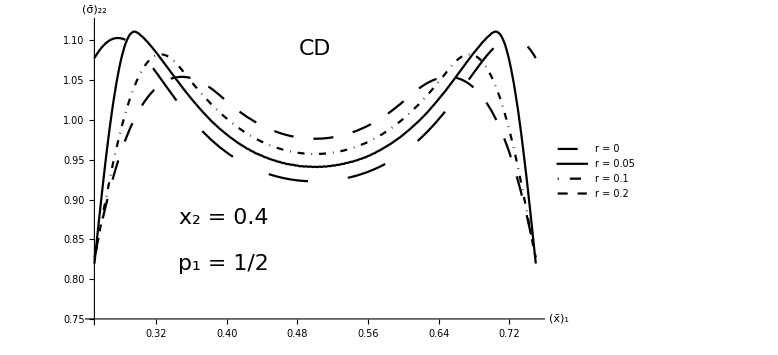

```mathematica
(*Export["CD_sigma_p12.eps",*)
Show[
Plot[{σ22Local[x,0.4],σ22Nonlocalr005p12[x,0.4],σ22Nonlocalr01p12[x,0.4],σ22Nonlocalr015p12[x,0.4]},{x,0.25,0.75},ImageSize->Large,PlotRange->{0.75,1.12},LabelStyle->Directive[{Black,FontSize->22}],AxesLabel->{"(x̄)_1","(σ̄)_22"},PlotStyle->{{Black,Dashing[0.05]},Black,{Black,DotDashed},{Black,Dashing[0.025]}},PlotLegends->Placed[{"r = 0","r = 0.05","r = 0.1","r = 0.2"},{Scaled[{0.65,0.05}], {0, 0}}]],
Graphics[{Text[Style["p_1 = 1/2",22],Scaled[{0.3,0.2}]],Text[Style["x_2 = 0.4",22],Scaled[{0.3,0.35}]],Text[Style["CD",22],Scaled[{0.5,0.9}]]}]
]
```

```mathematica
Export["T/CD_sigma_r01.eps",
Show[
Plot[{σ22Local[x,0.4],σ22Nonlocalr01p23[x,0.4],σ22Nonlocalr01p12[x,0.4],σ22Nonlocalr01p13[x,0.4]},{x,0.25,0.75},ImageSize->Large,PlotRange->{0.72,1.12},LabelStyle->Directive[{Black,FontSize->22}],AxesLabel->{"(x̄)_1","(σ̄)_22"},PlotStyle->{{Black,Dashing[0.05]},Black,{Black,DotDashed},{Black,Dashing[0.025]}},PlotLegends->Placed[{"p_1 = 1","p_1 = 2/3","p_1 = 1/2","p_1 = 1/3"},{Scaled[{0.65,0.05}], {0, 0}}]],
Graphics[{Text[Style["r = 0.1",22],Scaled[{0.3,0.3}]],Text[Style["x_2 = 0.4",22],Scaled[{0.3,0.45}]],Text[Style["φ = φ_(2, 1)",22],Scaled[{0.3,0.15}]],Text[Style["CD",22],Scaled[{0.5,0.9}]]}]
]]
```

T/CD_sigma_r01.eps

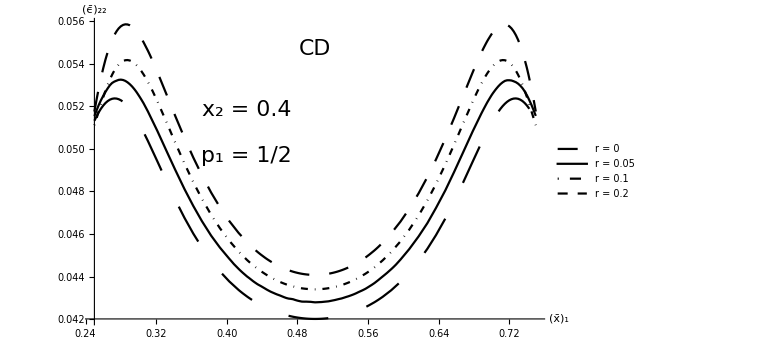

```mathematica
(*Export["CD_eps_p12.eps",*)
Show[
Plot[{ϵ22Local[x,0.4],ϵ22Nonlocalr005p12[x,0.4],ϵ22Nonlocalr01p12[x,0.4],ϵ22Nonlocalr015p12[x,0.4]},{x,0.25,0.75},ImageSize->Large,PlotRange->Full,LabelStyle->Directive[{Black,FontSize->22}],AxesLabel->{"(x̄)_1","(ϵ̄)_22"},PlotStyle->{{Black,Dashing[0.05]},Black,{Black,DotDashed},{Black,Dashing[0.025]}},PlotLegends->Placed[{"r = 0","r = 0.05","r = 0.1","r = 0.2"},{Scaled[{0.48,0.35}], {0, 0}}]],
Graphics[{Text[Style["p_1 = 1/2",22],Scaled[{0.35,0.55}]],Text[Style["x_2 = 0.4",22],Scaled[{0.35,0.7}]],Text[Style["CD",22],Scaled[{0.5,0.9}]]}]
]
```

```mathematica
Export["T/CD_eps_r01.eps",
Show[
Plot[{ϵ22Local[x,0.4],ϵ22Nonlocalr01p23[x,0.4],ϵ22Nonlocalr01p12[x,0.4],ϵ22Nonlocalr01p13[x,0.4]},{x,0.25,0.75},ImageSize->Large,PlotRange->{0.0415,0.056},LabelStyle->Directive[{Black,FontSize->22}],AxesLabel->{"(x̄)_1","(ϵ̄)_22"},PlotStyle->{{Black,Dashing[0.05]},Black,{Black,DotDashed},{Black,Dashing[0.025]}},PlotLegends->Placed[{"p_1 = 1","p_1 = 2/3","p_1 = 1/2","p_1 = 1/3"},{Scaled[{0.43,0.35}], {0, 0}}]],
Graphics[{Text[Style["r = 0.1",22],Scaled[{0.32,0.67}]],Text[Style["x_2 = 0.4",22],Scaled[{0.32,0.8}]],Text[Style["φ = φ_(2, 1)",22],Scaled[{0.33,0.55}]],Text[Style["CD",22],Scaled[{0.5,0.9}]]}]
]]
```

T/CD_eps_r01.eps

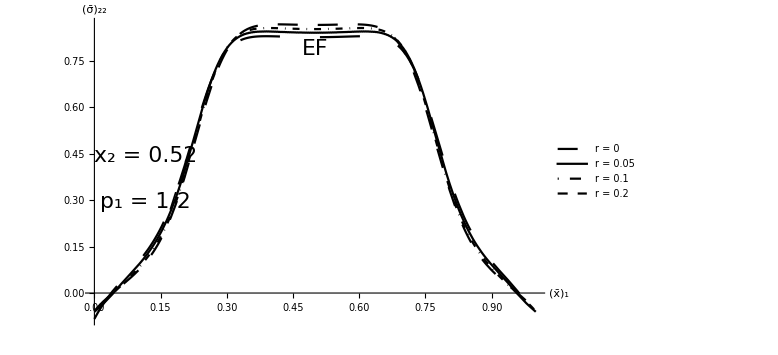

```mathematica
(*Export["EF_sigma_p12.eps",*)
y0=0.52;
y0=0.625;
Show[
Plot[{σ22Local[x,y0],σ22Nonlocalr005p12[x,y0],σ22Nonlocalr01p12[x,y0],σ22Nonlocalr015p12[x,y0]},{x,0,1},ImageSize->Large,PlotRange->Full,LabelStyle->Directive[{Black,FontSize->22}],AxesLabel->{"(x̄)_1","(σ̄)_22"},PlotStyle->{{Black,Dashing[0.05]},Black,{Black,DotDashed},{Black,Dashing[0.025]}},PlotLegends->Placed[{"r = 0","r = 0.05","r = 0.1","r = 0.2"},{Scaled[{0.77,0.25}], {0, 0}}]],
Graphics[{Text[Style["p_1 = 1/2",22],Scaled[{0.13,0.4}]],Text[Style["x_2 = 0.52",22],Scaled[{0.13,0.55}]],Text[Style["EF",22],Scaled[{0.5,0.9}]]}]
]
```

```mathematica
Export["T/EF_sigma_r01.eps",
Show[
Plot[{σ22Local[x,0.52],σ22Nonlocalr01p23[x,0.52],σ22Nonlocalr01p12[x,0.52],σ22Nonlocalr01p13[x,0.52]},{x,0,1},ImageSize->Large,PlotRange->Full,LabelStyle->Directive[{Black,FontSize->22}],AxesLabel->{"(x̄)_1","(σ̄)_22"},PlotStyle->{{Black,Dashing[0.05]},Black,{Black,DotDashed},{Black,Dashing[0.025]}},PlotLegends->Placed[{"p_1 = 1","p_1 = 2/3","p_1 = 1/2","p_1 = 1/3"},{Scaled[{0.77,0.25}], {0, 0}}]],
Graphics[{Text[Style["r = 0.1",22],Scaled[{0.13,0.55}]],Text[Style["x_2 = 0.52",22],Scaled[{0.13,0.7}]],Text[Style["φ = φ_(2, 1)",22],Scaled[{0.13,0.4}]],Text[Style["EF",22],Scaled[{0.5,0.9}]]}]
]
]
```

T/EF_sigma_r01.eps

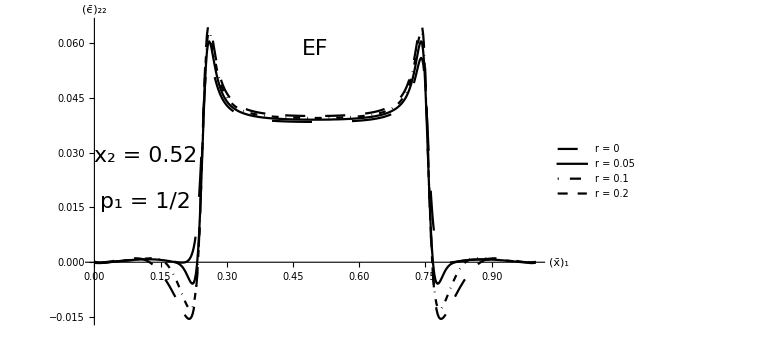

```mathematica
(*Export["EF_eps_p12.eps",*)
Show[
Plot[{ϵ22Local[x,0.52],ϵ22Nonlocalr005p12[x,0.52],ϵ22Nonlocalr01p12[x,0.52],ϵ22Nonlocalr015p12[x,0.52]},{x,0,1},ImageSize->Large,PlotRange->Full,LabelStyle->Directive[{Black,FontSize->22}],AxesLabel->{"(x̄)_1","(ϵ̄)_22"},PlotStyle->{{Black,Dashing[0.05]},Black,{Black,DotDashed},{Black,Dashing[0.025]}},PlotLegends->Placed[{"r = 0","r = 0.05","r = 0.1","r = 0.2"},{Scaled[{0.77,0.25}], {0, 0}}]],
Graphics[{Text[Style["p_1 = 1/2",22],Scaled[{0.13,0.4}]],Text[Style["x_2 = 0.52",22],Scaled[{0.13,0.55}]],Text[Style["EF",22],Scaled[{0.5,0.9}]]}]
]
```

```mathematica
Export["T/EF_eps_r01.eps",
Show[
Plot[{ϵ22Local[x,0.52],ϵ22Nonlocalr01p23[x,0.52],ϵ22Nonlocalr01p12[x,0.52],ϵ22Nonlocalr01p13[x,0.52]},{x,0,1},ImageSize->Large,PlotRange->Full,LabelStyle->Directive[{Black,FontSize->22}],AxesLabel->{"(x̄)_1","(ϵ̄)_22"},PlotStyle->{{Black,Dashing[0.05]},Black,{Black,DotDashed},{Black,Dashing[0.025]}},PlotLegends->Placed[{"p_1 = 1","p_1 = 2/3","p_1 = 1/2","p_1 = 1/3"},{Scaled[{0.75,0.3}], {0, 0}}]],
Graphics[{Text[Style["r = 0.1",22],Scaled[{0.13,0.7}]],Text[Style["x_2 = 0.52",22],Scaled[{0.13,0.85}]],Text[Style["φ = φ_(2, 1)",22],Scaled[{0.13,0.55}]],Text[Style["EF",22],Scaled[{0.5,0.9}]]}]
]
]
```

T/EF_eps_r01.eps

```mathematica
points={{-1,-1},{1,-1},{1,1},{-1,1},{-1,-1}};
N0=5;
PLeft=Table[Arrow[{{-1,n/N0},{-1-2/10,n/N0}}],{n,-N0,N0}];
PRight=Table[Arrow[{{1,n/N0},{1+2/10,n/N0}}],{n,-N0,N0}];
Ellipse=Circle[{0,0},{1/3,0.5}];
rx={Arrow[{{0,0},{1/3,0}}],Text[Style["R_1",22],{1/3-0.07,0.1}]};
ry={Arrow[{{0,0},{0,0.5}}],Text[Style["R_2",22],{0.07,0.5-0.1}]};
σn={Rotate[Text[Style["σ̄·n = -1",22],{-1.25,0}],π/2],Rotate[Text[Style["σ̄·n = 1",22],{1.25,0}],π/2]};
AB={Line[{{0,-1},{0,-0.5}}],Text[Style["A",22],{0,-1.1}],Text[Style["B",22],{0,-0.4}]};
AC={Circle[{0,0},{1/3,0.5},{0,π/2}],Text[Style["C",22],{1/3+0.1,0}],Text[Style["D",22],{0,0.6}]};
EF={Line[{{2/3,-1},{2/3,1}}],Text[Style["E",22],{2/3,-1.1}],Text[Style["F",22],{2/3,1.1}]};
ϕArrow={Arrow[BezierCurve[{{0.2,0},{0.2,0.2},{0,0.2}}]],Text[Style["φ",22],{0.1,0.1}]};
Export["EllipticalCut.eps",
Graphics[{Thick,Arrowheads[0.03],Line[points],PLeft,PRight,Ellipse,rx,ry,σn,AB,EF,ϕArrow,Thickness[0.01],AC},ImageSize->Large]]
```

EllipticalCut.eps

```mathematica
σ11Local=Interpolation[Import["data/circle/loc/sigma11.csv"]];
σ11Nonlocalr005p12=Interpolation[Import["data/circle/nonloc_p12_r005/sigma11.csv"]];
σ11Nonlocalr02p12=Interpolation[Import["data/circle/nonloc_p12_r02/sigma11.csv"]];
σ11Nonlocalr02p23=Interpolation[Import["data/circle/nonloc_p23_r02/sigma11.csv"]];
σ11Nonlocalr01p12=Interpolation[Import["data/circle/nonloc_p12_r01/sigma11.csv"]];
σ11Nonlocalr02p13=Interpolation[Import["data/circle/nonloc_p13_r02/sigma11.csv"]];
ϵ11Local=Interpolation[Import["data/circle/loc/eps11.csv"]];
ϵ11Nonlocalr005p12=Interpolation[Import["data/circle/nonloc_p12_r005/eps11.csv"]];
ϵ11Nonlocalr02p12=Interpolation[Import["data/circle/nonloc_p12_r02/eps11.csv"]];
ϵ11Nonlocalr02p23=Interpolation[Import["data/circle/nonloc_p23_r02/eps11.csv"]];
ϵ11Nonlocalr01p12=Interpolation[Import["data/circle/nonloc_p12_r01/eps11.csv"]];
ϵ11Nonlocalr02p13=Interpolation[Import["data/circle/nonloc_p13_r02/eps11.csv"]];
```

Interpolation::udeg: Interpolation on unstructured grids is currently only supported for InterpolationOrder->1 or InterpolationOrder->All. Order will be reduced to 1.

```mathematica
x0=0;
Export["circle/ABCircleEps.eps",
Show[
Plot[{ϵ11Local[x0,y],ϵ11Nonlocalr02p23[x0,y],ϵ11Nonlocalr02p12[x0,y],ϵ11Nonlocalr02p13[x0,y]},{y,-1,-0.2},PlotRange->Full,ImageSize->Large,LabelStyle->Directive[{Black,FontSize->22}],AxesLabel->{"(x̄)_2","(ϵ̄)_11"},PlotStyle->{{Black,Dashing[0.05]},Black,{Black,DotDashed},{Black,Dashing[0.025]}},PlotLegends->Placed[{"p_1 = 1","p_1 = 2/3","p_1 = 1/2","p_1 = 1/3"},{Scaled[{0.4,0.35}], {0, 0}}]],
Graphics[{Text[Style["r = 0.2",22],Scaled[{0.2,0.6}]],Text[Style["x_1 = 0",22],Scaled[{0.2,0.75}]],Text[Style["φ = φ_(2, 1)",22],Scaled[{0.2,0.45}]],Text[Style["AB",22],Scaled[{0.5,0.9}]]}]
]
]
```

circle/ABCircleEps.eps

```mathematica
x0=0;
Export["circle/ABCircleSigma.eps",
Show[
Plot[{σ11Local[x0,y],σ11Nonlocalr02p23[x0,y],σ11Nonlocalr02p12[x0,y],σ11Nonlocalr02p13[x0,y]},{y,-0.2,-1},PlotRange->Full,ImageSize->Large,LabelStyle->Directive[{Black,FontSize->22}],AxesLabel->{"(x̄)_2","(σ̄)_11"},PlotStyle->{{Black,Dashing[0.05]},Black,{Black,DotDashed},{Black,Dashing[0.025]}},PlotLegends->Placed[{"p_1 = 1","p_1 = 2/3","p_1 = 1/2","p_1 = 1/3"},{Scaled[{0.4,0.35}], {0, 0}}]],
Graphics[{Text[Style["r = 0.2",22],Scaled[{0.2,0.6}]],Text[Style["x_1 = 0",22],Scaled[{0.2,0.75}]],Text[Style["φ = φ_(2, 1)",22],Scaled[{0.2,0.45}]],Text[Style["AB",22],Scaled[{0.5,0.9}]]}]
]
]
```

circle/ABCircleSigma.eps

```mathematica
x0=0.6;
Export["circle/EFCircleEps.eps",
Show[
Plot[{ϵ11Local[x0,y],ϵ11Nonlocalr02p23[x0,y],ϵ11Nonlocalr02p12[x0,y],ϵ11Nonlocalr02p13[x0,y]},{y,-1,1},PlotRange->Full,ImageSize->Large,LabelStyle->Directive[{Black,FontSize->22}],AxesLabel->{"(x̄)_2","(ϵ̄)_11"},PlotStyle->{{Black,Dashing[0.05]},Black,{Black,DotDashed},{Black,Dashing[0.025]}},PlotLegends->Placed[{"p_1 = 1","p_1 = 2/3","p_1 = 1/2","p_1 = 1/3"},{Scaled[{0.65,0.15}], {0, 0}}]],
Graphics[{Text[Style["r = 0.2",22],Scaled[{0.2,0.4}]],Text[Style["x_1 = 0.6",22],Scaled[{0.2,0.55}]],Text[Style["φ = φ_(2, 1)",22],Scaled[{0.2,0.25}]],Text[Style["EF",22],Scaled[{0.5,0.9}]]}]
]
]
```

circle/EFCircleEps.eps

```mathematica
x0=0.6;
Export["circle/EFCircleSigma.eps",
Show[
Plot[{σ11Local[x0,y],σ11Nonlocalr02p23[x0,y],σ11Nonlocalr02p12[x0,y],σ11Nonlocalr02p13[x0,y]},{y,-1,1},PlotRange->Full,ImageSize->Large,LabelStyle->Directive[{Black,FontSize->22}],AxesLabel->{"(x̄)_2","(σ̄)_11"},PlotStyle->{{Black,Dashing[0.05]},Black,{Black,DotDashed},{Black,Dashing[0.025]}},PlotLegends->Placed[{"p_1 = 1","p_1 = 2/3","p_1 = 1/2","p_1 = 1/3"},{Scaled[{0.65,0.15}], {0, 0}}]],
Graphics[{Text[Style["r = 0.2",22],Scaled[{0.2,0.4}]],Text[Style["x_1 = 0.6",22],Scaled[{0.2,0.55}]],Text[Style["φ = φ_(2, 1)",22],Scaled[{0.2,0.25}]],Text[Style["EF",22],Scaled[{0.5,0.9}]]}]
]
]
```

circle/EFCircleSigma.eps

```mathematica
X[ϕ]=0.2Cos[ϕ];
Y[ϕ]=0.2Sin[ϕ];
```

```mathematica
Export["circle/CDCircleEps.eps",
Show[
Plot[{ϵ11Local[X[ϕ],Y[ϕ]],ϵ11Nonlocalr02p23[X[ϕ],Y[ϕ]],ϵ11Nonlocalr02p12[X[ϕ],Y[ϕ]],ϵ11Nonlocalr02p13[X[ϕ],Y[ϕ]]},{ϕ,0,π/2},ImageSize->Large,PlotRange->Full,LabelStyle->Directive[{Black,FontSize->22}],AxesLabel->{"φ","(ϵ̄)_11"},PlotStyle->{{Black,Dashing[0.05]},Black,{Black,DotDashed},{Black,Dashing[0.025]}},PlotLegends->Placed[{"p_1 = 1","p_1 = 2/3","p_1 = 1/2","p_1 = 1/3"},{Scaled[{0.3,0.3}], {0, 0}}]],
Graphics[{Text[Style["r = 0.2",22],Scaled[{0.15,0.7}]],Text[Style["φ = φ_(2, 1)",22],Scaled[{0.15,0.45}]],Text[Style["CD",22],Scaled[{0.5,0.9}]]}]
]
]
```

circle/CDCircleEps.eps

```mathematica
Export["circle/CDCircleSigma.eps",
Show[
Plot[{σ11Local[X[ϕ],Y[ϕ]],σ11Nonlocalr02p23[X[ϕ],Y[ϕ]],σ11Nonlocalr02p12[X[ϕ],Y[ϕ]],σ11Nonlocalr02p13[X[ϕ],Y[ϕ]]},{ϕ,0,π/2},ImageSize->Large,PlotRange->Full,LabelStyle->Directive[{Black,FontSize->22}],AxesLabel->{"φ","(σ̄)_11"},PlotStyle->{{Black,Dashing[0.05]},Black,{Black,DotDashed},{Black,Dashing[0.025]}},PlotLegends->Placed[{"p_1 = 1","p_1 = 2/3","p_1 = 1/2","p_1 = 1/3"},{Scaled[{0.3,0.35}], {0, 0}}]],
Graphics[{Text[Style["r = 0.2",22],Scaled[{0.15,0.7}]],Text[Style["φ = φ_(2, 1)",22],Scaled[{0.15,0.5}]],Text[Style["CD",22],Scaled[{0.5,0.9}]]}]
]
]
```

circle/CDCircleSigma.eps

```mathematica
σ11E23Local=Interpolation[Import["data/ellipse23/loc/sigma11.csv"]];
σ11E23Nonlocalr005p12=Interpolation[Import["data/ellipse23/nonloc_p12_r005/sigma11.csv"]];
σ11E23Nonlocalr02p12=Interpolation[Import["data/ellipse23/nonloc_p12_r02/sigma11.csv"]];
σ11E23Nonlocalr02p23=Interpolation[Import["data/ellipse23/nonloc_p23_r02/sigma11.csv"]];
σ11E23Nonlocalr01p12=Interpolation[Import["data/ellipse23/nonloc_p12_r01/sigma11.csv"]];
σ11E23Nonlocalr02p13=Interpolation[Import["data/ellipse23/nonloc_p13_r02/sigma11.csv"]];
ϵ11E23Local=Interpolation[Import["data/ellipse23/loc/eps11.csv"]];
ϵ11E23Nonlocalr005p12=Interpolation[Import["data/ellipse23/nonloc_p12_r005/eps11.csv"]];
ϵ11E23Nonlocalr02p12=Interpolation[Import["data/ellipse23/nonloc_p12_r02/eps11.csv"]];
ϵ11E23Nonlocalr02p23=Interpolation[Import["data/ellipse23/nonloc_p23_r02/eps11.csv"]];
ϵ11E23Nonlocalr01p12=Interpolation[Import["data/ellipse23/nonloc_p12_r01/eps11.csv"]];
ϵ11E23Nonlocalr02p13=Interpolation[Import["data/ellipse23/nonloc_p13_r02/eps11.csv"]];
```

Interpolation::udeg: Interpolation on unstructured grids is currently only supported for InterpolationOrder->1 or InterpolationOrder->All. Order will be reduced to 1.

```mathematica
σ11E12Local=Interpolation[Import["data/ellipse12/loc/sigma11.csv"]];
σ11E12Nonlocalr005p12=Interpolation[Import["data/ellipse12/nonloc_p12_r005/sigma11.csv"]];
σ11E12Nonlocalr02p12=Interpolation[Import["data/ellipse12/nonloc_p12_r02/sigma11.csv"]];
σ11E12Nonlocalr02p23=Interpolation[Import["data/ellipse12/nonloc_p23_r02/sigma11.csv"]];
σ11E12Nonlocalr01p12=Interpolation[Import["data/ellipse12/nonloc_p12_r01/sigma11.csv"]];
σ11E12Nonlocalr02p13=Interpolation[Import["data/ellipse12/nonloc_p13_r02/sigma11.csv"]];
ϵ11E12Local=Interpolation[Import["data/ellipse12/loc/eps11.csv"]];
ϵ11E12Nonlocalr005p12=Interpolation[Import["data/ellipse12/nonloc_p12_r005/eps11.csv"]];
ϵ11E12Nonlocalr02p12=Interpolation[Import["data/ellipse12/nonloc_p12_r02/eps11.csv"]];
ϵ11E12Nonlocalr02p23=Interpolation[Import["data/ellipse12/nonloc_p23_r02/eps11.csv"]];
ϵ11E12Nonlocalr01p12=Interpolation[Import["data/ellipse12/nonloc_p12_r01/eps11.csv"]];
ϵ11E12Nonlocalr02p13=Interpolation[Import["data/ellipse12/nonloc_p13_r02/eps11.csv"]];
```

Interpolation::udeg: Interpolation on unstructured grids is currently only supported for InterpolationOrder->1 or InterpolationOrder->All. Order will be reduced to 1.

```mathematica
σ11E13Local=Interpolation[Import["data/ellipse13/loc/sigma11.csv"]];
σ11E13Nonlocalr005p12=Interpolation[Import["data/ellipse13/nonloc_p12_r005/sigma11.csv"]];
σ11E13Nonlocalr02p12=Interpolation[Import["data/ellipse13/nonloc_p12_r02/sigma11.csv"]];
σ11E13Nonlocalr02p23=Interpolation[Import["data/ellipse13/nonloc_p23_r02/sigma11.csv"]];
σ11E13Nonlocalr01p12=Interpolation[Import["data/ellipse13/nonloc_p12_r01/sigma11.csv"]];
σ11E13Nonlocalr02p13=Interpolation[Import["data/ellipse13/nonloc_p13_r02/sigma11.csv"]];
ϵ11E13Local=Interpolation[Import["data/ellipse13/loc/eps11.csv"]];
ϵ11E13Nonlocalr005p12=Interpolation[Import["data/ellipse13/nonloc_p12_r005/eps11.csv"]];
ϵ11E13Nonlocalr02p12=Interpolation[Import["data/ellipse13/nonloc_p12_r02/eps11.csv"]];
ϵ11E13Nonlocalr02p23=Interpolation[Import["data/ellipse13/nonloc_p23_r02/eps11.csv"]];
ϵ11E13Nonlocalr01p12=Interpolation[Import["data/ellipse13/nonloc_p12_r01/eps11.csv"]];
ϵ11E13Nonlocalr02p13=Interpolation[Import["data/ellipse13/nonloc_p13_r02/eps11.csv"]];
```

Interpolation::udeg: Interpolation on unstructured grids is currently only supported for InterpolationOrder->1 or InterpolationOrder->All. Order will be reduced to 1.

```mathematica
x0=0;
Export["circle/ABDiffR1Loc.eps",
Show[
Plot[{σ11Local[x0,y],σ11E23Local[x0,y],σ11E12Local[x0,y],σ11E13Local[x0,y]},{y,-1,-0.2},PlotRange->Full,ImageSize->Large,LabelStyle->Directive[{Black,FontSize->22}],AxesLabel->{"(x̄)_2","(σ̄)_11"},PlotStyle->{{Black,Dashing[0.05]},Black,{Black,DotDashed},{Black,Dashing[0.025]}},PlotLegends->Placed[{"R_1 = R_2","R_1 = 2/3 R_2","R_1 = 1/2 R_2","R_1 = 1/3 R_2"},{Scaled[{0.4,0.32}], {0, 0}}]],
Graphics[{Text[Style["r = 0",22],Scaled[{0.2,0.52}]],Text[Style["p_1 = 1",22],Scaled[{0.2,0.64}]],Text[Style["x_1 = 0",22],Scaled[{0.2,0.76}]],Text[Style["φ = φ_(2, 1)",22],Scaled[{0.2,0.4}]],Text[Style["AB",22],Scaled[{0.5,0.9}]]}]
]
]
```

circle/ABDiffR1Loc.eps

```mathematica
x0=0;
Export["circle/ABDiffR1NonLoc.eps",
Show[
Plot[{σ11Nonlocalr01p12[x0,y],σ11E23Nonlocalr01p12[x0,y],σ11E12Nonlocalr01p12[x0,y],σ11E13Nonlocalr01p12[x0,y]},{y,-1,-0.2},PlotRange->Full,ImageSize->Large,LabelStyle->Directive[{Black,FontSize->22}],AxesLabel->{"(x̄)_2","(σ̄)_11"},PlotStyle->{{Black,Dashing[0.05]},Black,{Black,DotDashed},{Black,Dashing[0.025]}},
PlotLegends->Placed[{"R_1 = R_2","R_1 = 2/3 R_2","R_1 = 1/2 R_2","R_1 = 1/3 R_2"},{Scaled[{0.4,0.32}], {0, 0}}]],
Graphics[{Text[Style["r = 0.1",22],Scaled[{0.2,0.52}]],Text[Style["p_1 = 1/2",22],Scaled[{0.2,0.64}]],Text[Style["x_1 = 0",22],Scaled[{0.2,0.76}]],Text[Style["φ = φ_(2, 1)",22],Scaled[{0.2,0.4}]],Text[Style["AB",22],Scaled[{0.5,0.9}]]}]
]
]
```

circle/ABDiffR1NonLoc.eps

```mathematica
f[ϕ_,a_,b_]:=b EllipticE[π FractionalPart[ϕ/π],1-a^2/b^2]+(b EllipticE[1-a^2/b^2]+a EllipticE[1-b^2/a^2]) IntegerPart[ϕ/π];
circle=Interpolation[Table[{ϕ,f[ϕ,0.2,0.2]/f[π/2,0.2,0.2]},{ϕ,0,π/2,π/2000}]];
ellipse23=Interpolation[Table[{ϕ,f[ϕ,0.4/3,0.2]/f[π/2,0.4/3,0.2]},{ϕ,0,π/2,π/2000}]];
ellipse12=Interpolation[Table[{ϕ,f[ϕ,0.1,0.2]/f[π/2,0.1,0.2]},{ϕ,0,π/2,π/2000}]];
ellipse13=Interpolation[Table[{ϕ,f[ϕ,0.2/3,0.2]/f[π/2,0.2/3,0.2]},{ϕ,0,π/2,π/2000}]];
ΦC=Interpolation[Table[{z,(x/.NSolve[circle[x]==z,x])⟦1⟧},{z,0,1,0.001}]];
Φ23=Interpolation[Table[{z,(x/.NSolve[ellipse23[x]==z,x])⟦1⟧},{z,0,1,0.001}]];
Φ12=Interpolation[Table[{z,(x/.NSolve[ellipse12[x]==z,x])⟦1⟧},{z,0,1,0.001}]];
Φ13=Interpolation[Table[{z,(x/.NSolve[ellipse13[x]==z,x])⟦1⟧},{z,0,1,0.001}]];
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of NSolve::ifun will be suppressed during this calculation.

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of NSolve::ifun will be suppressed during this calculation.

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of NSolve::ifun will be suppressed during this calculation.

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of NSolve::ifun will be suppressed during this calculation.

```mathematica
Export["circle/CDEpsLoc.eps",
Show[
Plot[{
ϵ11Local[0.2Cos[ΦC[x]],0.2Sin[ΦC[x]]],
ϵ11E23Local[0.4/3 Cos[Φ23[x]],0.2Sin[Φ23[x]]],
ϵ11E12Local[0.1Cos[Φ12[x]],0.2Sin[Φ12[x]]],
ϵ11E13Local[0.2/3 Cos[Φ13[x]],0.2Sin[Φ13[x]]]
},{x,0,1},ImageSize->Large,PlotRange->Full,LabelStyle->Directive[{Black,FontSize->22}],AxesLabel->{"s","(ϵ̄)_11"},PlotStyle->{{Black,Dashing[0.05]},Black,{Black,DotDashed},{Black,Dashing[0.025]}},PlotLegends->Placed[{"R_1 = R_2","R_1 = 2/3 R_2","R_1 = 1/2 R_2","R_1 = 1/3 R_2"},{Scaled[{0.35,0.3}], {0, 0}}]],
Graphics[{Text[Style["r = 0",22],Scaled[{0.2,0.7}]],Text[Style["p_1 = 1",22],Scaled[{0.2,0.55}]],Text[Style["φ = φ_(2, 1)",22],Scaled[{0.2,0.4}]],Text[Style["CD",22],Scaled[{0.5,0.9}]]}]
]
]
```

circle/CDEpsLoc.eps

```mathematica
Export["circle/CDEpsNonLoc.eps",
Show[
Plot[{
ϵ11Nonlocalr02p12[0.2Cos[ΦC[x]],0.2Sin[ΦC[x]]],
ϵ11E23Nonlocalr02p12[0.4/3 Cos[Φ23[x]],0.2Sin[Φ23[x]]],
ϵ11E12Nonlocalr02p12[0.1Cos[Φ12[x]],0.2Sin[Φ12[x]]],
ϵ11E13Nonlocalr02p12[0.2/3 Cos[Φ13[x]],0.2Sin[Φ13[x]]]
},{x,0,1},ImageSize->Large,PlotRange->Full,LabelStyle->Directive[{Black,FontSize->22}],AxesLabel->{"s","(ϵ̄)_11"},PlotStyle->{{Black,Dashing[0.05]},Black,{Black,DotDashed},{Black,Dashing[0.025]}},PlotLegends->Placed[{"R_1 = R_2","R_1 = 2/3 R_2","R_1 = 1/2 R_2","R_1 = 1/3 R_2"},{Scaled[{0.35,0.3}], {0, 0}}]],
Graphics[{Text[Style["r = 0",22],Scaled[{0.2,0.7}]],Text[Style["p_1 = 1",22],Scaled[{0.2,0.55}]],Text[Style["φ = φ_(2, 1)",22],Scaled[{0.2,0.4}]],Text[Style["CD",22],Scaled[{0.5,0.9}]]}]
]
]
```

circle/CDEpsNonLoc.eps

```mathematica
Export["circle/CDSigmaLoc.eps",
Show[
Plot[{
(*
Labeled[σ11Local[0.2Cos[ΦC[x]],0.2Sin[ΦC[x]]],ToString[ SetPrecision[σ11Local[0.2Cos[ΦC[1]],0.2Sin[ΦC[1]]],2]],{Scaled[1],Top}],
Labeled[σ11E23Local[0.4/3 Cos[Φ23[x]],0.2Sin[Φ23[x]]],ToString[ SetPrecision[σ11E23Local[0.4/3 Cos[Φ23[1]],0.2Sin[Φ23[1]]],2]],{Scaled[1],Top}],
Labeled[σ11E12Local[0.1Cos[Φ12[x]],0.2Sin[Φ12[x]]],ToString[ SetPrecision[σ11E12Local[0.1Cos[Φ12[1]],0.2Sin[Φ12[1]]],2]],{Scaled[1],Top}],
Labeled[σ11E13Local[0.2/3 Cos[Φ13[x]],0.2Sin[Φ13[x]]],ToString[ SetPrecision[σ11E13Local[0.2/3 Cos[Φ13[1]],0.2Sin[Φ13[1]]],2]],{Scaled[0.95],Above}]
*)
σ11Local[0.2Cos[ΦC[x]],0.2Sin[ΦC[x]]],σ11E23Local[0.4/3 Cos[Φ23[x]],0.2Sin[Φ23[x]]],σ11E12Local[0.1Cos[Φ12[x]],0.2Sin[Φ12[x]]],σ11E13Local[0.2/3 Cos[Φ13[x]],0.2Sin[Φ13[x]]]
},{x,0,1},ImageSize->Large,PlotRange->Full,LabelStyle->Directive[{Black,FontSize->22}],AxesLabel->{"s","(σ̄)_11"},PlotStyle->{{Black,Dashing[0.05]},Black,{Black,DotDashed},{Black,Dashing[0.025]}},PlotLegends->Placed[{"R_1 = R_2","R_1 = 2/3 R_2","R_1 = 1/2 R_2","R_1 = 1/3 R_2"},{Scaled[{0.35,0.3}], {0, 0}}]],
Graphics[{Text[Style["r = 0",22],Scaled[{0.2,0.7}]],Text[Style["p_1 = 1",22],Scaled[{0.2,0.55}]],Text[Style["φ = φ_(2, 1)",22],Scaled[{0.2,0.4}]],Text[Style["CD",22],Scaled[{0.5,0.9}]]}]
]
]
```

circle/CDSigmaLoc.eps

```mathematica
Export["circle/CDSigmaNonLoc.eps",
Show[
Plot[{
(*
Labeled[σ11Nonlocalr01p12[0.2Cos[ΦC[x]],0.2Sin[ΦC[x]]],ToString[ SetPrecision[σ11Nonlocalr01p12[0.2Cos[ΦC[1]],0.2Sin[ΦC[1]]],2]],{Scaled[1],Top}],
Labeled[σ11E23Nonlocalr01p12[0.4/3 Cos[Φ23[x]],0.2Sin[Φ23[x]]],ToString[ SetPrecision[σ11E23Nonlocalr01p12[0.4/3 Cos[Φ23[1]],0.2Sin[Φ23[1]]],2]],{Scaled[1],Top}],
Labeled[σ11E12Nonlocalr01p12[0.1Cos[Φ12[x]],0.2Sin[Φ12[x]]],ToString[ SetPrecision[σ11E12Nonlocalr01p12[0.1Cos[Φ12[1]],0.2Sin[Φ12[1]]],2]],{Scaled[1],Top}],
Labeled[σ11E13Nonlocalr01p12[0.2/3 Cos[Φ13[x]],0.2Sin[Φ13[x]]],ToString[ SetPrecision[σ11E13Nonlocalr01p12[0.2/3 Cos[Φ13[1]],0.2Sin[Φ13[1]]],2]],{Scaled[0.95],Above}]
*)
σ11Nonlocalr01p12[0.2Cos[ΦC[x]],0.2Sin[ΦC[x]]],σ11E23Nonlocalr01p12[0.4/3 Cos[Φ23[x]],0.2Sin[Φ23[x]]],σ11E12Nonlocalr01p12[0.1Cos[Φ12[x]],0.2Sin[Φ12[x]]],σ11E13Nonlocalr01p12[0.2/3 Cos[Φ13[x]],0.2Sin[Φ13[x]]]
},{x,0,1},ImageSize->Large,PlotRange->Full,LabelStyle->Directive[{Black,FontSize->22}],AxesLabel->{"s","(σ̄)_11"},PlotStyle->{{Black,Dashing[0.05]},Black,{Black,DotDashed},{Black,Dashing[0.025]}},PlotLegends->Placed[{"R_1 = R_2","R_1 = 2/3 R_2","R_1 = 1/2 R_2","R_1 = 1/3 R_2"},{Scaled[{0.35,0.3}], {0, 0}}]],
Graphics[{Text[Style["r = 0",22],Scaled[{0.2,0.7}]],Text[Style["p_1 = 1",22],Scaled[{0.2,0.55}]],Text[Style["φ = φ_(2, 1)",22],Scaled[{0.2,0.4}]],Text[Style["CD",22],Scaled[{0.5,0.9}]]}]
]
]
```

circle/CDSigmaNonLoc.eps

```mathematica
Export["MaxSigma.eps",
ListLinePlot[
{
{{1,3.4},{3/2,4.4},{2,5.4},{3,7.6}},
{{1,2.8},{3/2,3.7},{2,4.7},{3,6.5}},
{{1,2.5},{3/2,3.3},{2,4.1},{3,5.7}},
{{1,2.2},{3/2,2.9},{2,3.6},{3,5}}
},
PlotRange->{2,8},
ImageSize->Large,
LabelStyle->Directive[{Black,FontSize->22}],
PlotLegends->Placed[{"p_1 = 1","p_1 = 2/3","p_1 = 1/2","p_1 = 1/3"},{Scaled[{0.1,0.5}], {0, 0}}],
AxesLabel->{"R_2/R_1","(σ̄)_11^max"},
PlotTheme->"Monochrome",
PlotStyle->{{Black,Dashing[0.05]},{Black,AbsoluteThickness[2],AbsoluteDashing[{}]},{Black,DotDashed},{Black,Dashing[0.025]}}
]]
```

MaxSigma.eps

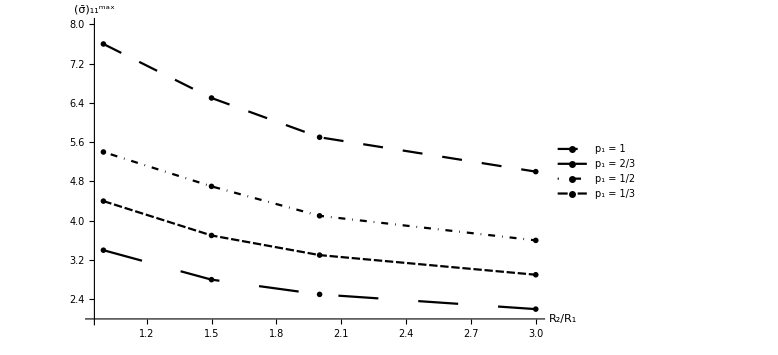

```mathematica
ListLinePlot[
{
{{1,3.4},{3/2,2.8},{2,2.5},{3,2.2}},
{{1,4.4},{3/2,3.7},{2,3.3},{3,2.9}},
{{1,5.4},{3/2,4.7},{2,4.1},{3,3.6}},
{{1,7.6},{3/2,6.5},{2,5.7},{3,5}}
},
PlotRange->{2,8},
ImageSize->Large,
LabelStyle->Directive[{Black,FontSize->22}],
PlotLegends->Placed[{"p_1 = 1","p_1 = 2/3","p_1 = 1/2","p_1 = 1/3"},{Scaled[{0.1,0.5}], {0, 0}}],
AxesLabel->{"R_2/R_1","(σ̄)_11^max"},
PlotTheme->"Monochrome",
PlotStyle->{{Black,Dashing[0.05]},Black,{Black,DotDashed},{Black,Dashing[0.025]}}
]
```

```mathematica
Export["QuadraticSerendipity.eps",
Graphics[{
Line[{{-1,-1},{1,-1},{1,1},{-1,1},{-1,-1}}],
PointSize[0.05],Point[{-1,-1}],Point[{0,-1}],Point[{1,-1}],Point[{1,0}],Point[{1,1}],Point[{0,1}],Point[{-1,1}],Point[{-1,0}],
Text[Style[1,Large],{-0.8,-0.8}],Text[Style[2,Large],{0,-0.8}],Text[Style[3,Large],{0.8,-0.8}],Text[Style[4,Large],{0.8,0}],Text[Style[5,Large],{0.8,0.8}],Text[Style[6,Large],{0,0.8}],Text[Style[7,Large],{-0.8,0.8}],Text[Style[8,Large],{-0.8,0}],
Thickness[0.01],Arrow[{{0,0},{0.5,0}}],Arrow[{{0,0},{0,0.5}}],
Text[Style[ξ,Large],{0.45,0.15}],Text[Style[η,Large],{0.15,0.45}]
}]
]
```

QuadraticSerendipity.eps

```mathematica
Export["Iterations.eps",
ListLinePlot[
{
{{-1/3,2410},{-1/4,2085},{-1/6,1938},{-1/12,1736},{0,1514},{1/12,1558},{1/6,1485},{1/4,1591},{1/3,1511},{5/12,1618},{1/2,1560}},
{{-1/3,2014},{-1/4,1810},{-1/6,1620},{-1/12,1451},{0,1314},{1/12,1227},{1/6,1240},{1/4,1252},{1/3,1262},{5/12,1274},{1/2,1306}},
{{-1/3,1755},{-1/4,1577},{-1/6,1411},{-1/12,1345},{0,1217},{1/12,1136},{1/6,1079},{1/4,1160},{1/3,1170},{5/12,1181},{1/2,1210}},
{{-1/3,1543},{-1/4,1387},{-1/6,1241},{-1/12,1112},{0,1006},{1/12,938},{1/6,948},{1/4,958},{1/3,966},{5/12,974},{1/2,999}}
},
ImageSize->Large,
PlotRange->{900, 2500},
LabelStyle->Directive[{Black,FontSize->22}],
PlotLegends->Placed[{"p_1 = 1","p_1 = 2/3","p_1 = 1/2","p_1 = 1/3"},{Scaled[{0.75,0.55}], {0, 0}}],
AxesLabel->{"s","Iterations"},
PlotTheme->"Monochrome",
PlotStyle->{{Black,Dashing[0.05]},{Black,AbsoluteThickness[2],AbsoluteDashing[{}]},{Black,DotDashed},{Black,Dashing[0.025]}}
]]
```

Iterations.eps